# Unidad 1 3 - Funciones

## Conceptos básicos

A veces es conveniente aislar una sección del código con el fin de que éste sea reutilizable. Para hacer esto se pueden utilizar funciones. En concepto de función en programación es similar al de matemáticas en el caso de las funciones puras, es decir, con una función se puede mapear un conjunto de números a otro conjunto. Por ejemplo, se podría definir una función que realiza la operación x^2+y^2, donde x y y son los argumentos.

```mathematica
f[x_,y_]:=x^2+y^2;
```

Para llamar a la función se hace lo siguiente,

```mathematica
f[2,9]
```

85

```mathematica
f[1.1,2.3]
```

6.5

```mathematica
f[1+I,4]
```

16+2 ⅈ

Cabe resaltar que con una definición de la función se puede operar sobre varios conjuntos de números, como en el ejemplo anterior que la función se llamó con argumentos enteros, decimales y complejos.
Esta función que se acaba de crear es una función que en la jerga de ciencias de la computación se denomina función pura, esto es una función que lo único que realiza es operar sobre los argumentos y devolver un número. Una función puede hacer más que eso. Es posible que una función durante su operación modifique el valor de alguna variable.

```mathematica
variableExterna= 8;

FuncionImpura[x_]:=Block[{},
variableExterna= 1;
Return[x^2];
];
```

```mathematica
variableExterna
```

8

```mathematica
FuncionImpura[3]
```

9

```mathematica
variableExterna
```

1

La función impura cambió el valor de la variable externa durante su operación.
A veces es conveniente que las variables que están definidas dentro de una función no sean las mismas que las que se definen afuera de la función. Para esto es útil declarar en Block las variables que deben bloquearse.
La función Block sirve para que las definiciones que se realizan en su interior (y que se han declarado como protegidas) no se confundan con las definiciones que vienen desde el exterior.

```mathematica
variable = 5;

Funcion[x_]:=Block[{variable},
variable= 1;
Print["Variable dentro de Block: "<>ToString[variable]];
Return[x^2];
];

Funcion[7.1]
Print["Variable afuera de Block: "<>ToString[variable]];
```

Variable dentro de Block: 1

50.41

Variable afuera de Block: 5

Ejercicio

Crear una función que resuelva una ecuación cuadrática por medio de la chicharronera. La función puede restringirse a una sola solución.

## Construcción de listas a partir de funciones

Una manera convencional de crear listas a partir de funciones es utilizando tablas.

```mathematica
f[x_]:= x^3;
Table[{x,f[x]},{x,0,1,0.1}]
```

{{0.,0.},{0.1,0.001},{0.2,0.008},{0.3,0.027},{0.4,0.064},{0.5,0.125},{0.6,0.216},{0.7,0.343},{0.8,0.512},{0.9,0.729},{1.,1.}}

Pero a veces nos interesa construir una tabla utilizando valores ya calculados. Como por ejemplo utilizar una función anidada.

```mathematica
Clear[f];
NestList[f,x,6]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]],f[f[f[f[f[x]]]]],f[f[f[f[f[f[x]]]]]]}

Un ejemplo: Se hará una función anidada que le sume 2 al argumento.

```mathematica
f[x_]:=x+2;
NestList[f,1,6]
```

{1,3,5,7,9,11,13}

A veces es más útil utilizar la notación de funciones puras, que tiene la ventaja de que se puede poner directamente como argumento en vez de definirlo.

```mathematica
NestList[#+2 &,1,6]
```

{1,3,5,7,9,11,13}

```mathematica
NestList[#^2 &,1.1,6]
```

{1.1,1.21,1.4641,2.14359,4.59497,21.1138,445.792}

Ejercicio:

Obtener 30 iteraciones del mapeo logístico, que está dado por la fórmula recurrente x_(n+1) = r x_n (1-x_n). Para este caso se utilizará r = 4. Graficar la órbita que se obtiene.

```mathematica
log = NestList[4 # (1-#)&,0.26,30]
```

{0.26,0.7696,0.709263,0.824835,0.577928,0.975709,0.0948039,0.343264,0.901736,0.354433,0.915241,0.310299,0.856054,0.492903,0.999799,0.000805748,0.0032204,0.0128401,0.0507009,0.192521,0.621827,0.940632,0.223373,0.693909,0.849596,0.511129,0.999505,0.00198076,0.00790734,0.0313793,0.121578}

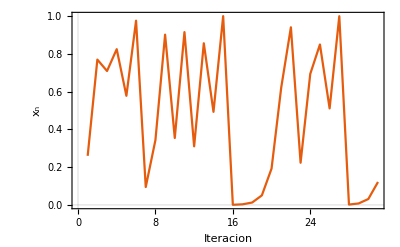

```mathematica
ListLinePlot[log,PlotTheme->"Scientific",FrameLabel->{"Iteracion","x_n"},BaseStyle->FontSize->14]
```

Ahora se hará un mapa de todos los puntos obtenidos de iterar la fórmula recurrente que describe al mapeo logístico pero haciendo variar el parámetro r.

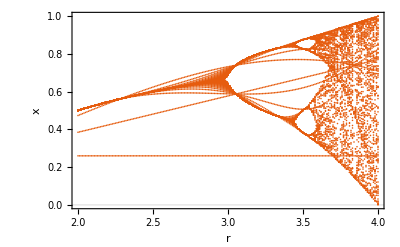

```mathematica
logisticmap = Table[
Transpose[{ConstantArray[r,101],NestList[r # (1-#)&,0.26,100]}]
,{r,2,4,0.01}];
logisticmap = Flatten[logisticmap,1];
ListPlot[logisticmap,PlotTheme->"Scientific",FrameLabel->{"r","x"},BaseStyle->FontSize->14]
```

Esta gráfica tiene mucho puntos que son dependientes de la condición inicial elegida. Para mejorarla se pueden realizar 200 iteraciones y descartar las 100 primeras.

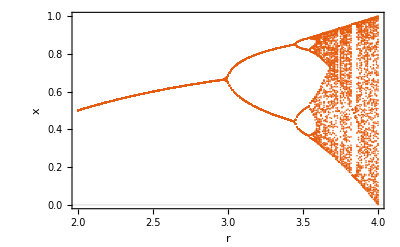

```mathematica
logisticmap = Table[
Transpose[{ConstantArray[r,101],Drop[NestList[r # (1-#)&,0.26,200],100]}]
,{r,2,4,0.01}];
logisticmap = Flatten[logisticmap,1];
ListPlot[logisticmap,PlotTheme->"Scientific",FrameLabel->{"r","x"},BaseStyle->FontSize->14]
```

Ejercicio

Una función que genera números aleatorios de forma iterativa es

```mathematica
LCG[x_,a_,c_,m_]:= Mod[a x + c,m];
```

Este algoritmo se conoce como Lineal Congruential Generator y la calidad de sus resultados depende de los parámetros a, c y m. En el compilador de GNU (que es el que utilizan la mayoría de los proyectos de software libre) la función que genera números aleatorios utiliza los parámetros a = 1103515245, c = 12345, y m = 2^31.

1) Generar una secuencia de aleatorios utilizando estos parámetros.
2) En 1960 IBM creó una computadora cuyo generador de números aleatorios utilizaba los parámetros a = 65539, c = 0, y m = 2^31 (Algoritmo RANDU). Estos parámetros dieron lugar a un generador de aleatorios de muy mala calidad que causó que numerosos artículos científicos que dependían de números aleatorios fueran publicados con errores. El ejercicio es generar una lista de números aleatorios usando RANDU, luego la lista se particionará de tres en tres usando la función partition, por ejemplo

```mathematica
Partition[{a,b,c,d,e,f,g,e,h,i,j,k,l,m,n,o},3]
```

{{a,b,c},{d,e,f},{g,e,h},{i,j,k},{l,m,n}}

Por último se deberá graficar los resultados en una gráfica tridimensional ListPointPlot3D.

Ejercicio

1) Implementar el método de Newton-Rhapson que está definido por la relación de recurrencia

x_(n+1) = x_n - (f(x_n))/(f'(x_n)).

La función que se resolverá son las raíces de f(x) = Cos(x) - x = 0. La condición inicial será x_0 = 2 y se harán 10 iteraciones. Graficar la convergencia del resultado.

2) Probar con la condición inicial x_0=-100.

```mathematica
f[x_]:= Cos[x]-x;
NewtonRhapson[x_]:= N[x- f[x]/f'[x]];
```

```mathematica
r = NestList[NewtonRhapson,2,10]
```

{2,0.734536,0.73909,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085}

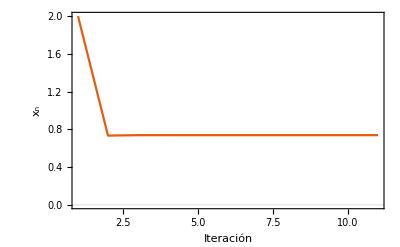

```mathematica
ListLinePlot[r,PlotRange->Full,PlotTheme->"Scientific", FrameLabel->{"Iteración","x_n"},BaseStyle->FontSize->14]
```

## Análisis de la convergencia de las condiciones iniciales del método de Newton-Rhapson

Cuando se encuentran las raíces de una función por el Método de Newton-Rhapson no se puede conocer de antemano a cuál raíz converge. Ahora se verificará la convergencia de las soluciones de la función

f(x) = z^3-1 = 0.

El procedimiento es el siguiente. Se desea iterar muchas condiciones iniciales en el plano complejo y ver a dónde converge cada una. Para esto primero se construye una tabla con condiciones iniciales complejas.

```mathematica
δ = 0.01;
z = Table[x+ⅈ y,{x,-2,2,δ},{y,-2,2,δ}]
```

{{-2.-2. ⅈ,-2.-1.99 ⅈ,-2.-1.98 ⅈ,-2.-1.97 ⅈ,-2.-1.96 ⅈ,-2.-1.95 ⅈ,-2.-1.94 ⅈ,-2.-1.93 ⅈ,-2.-1.92 ⅈ,-2.-1.91 ⅈ,-2.-1.9 ⅈ,-2.-1.89 ⅈ,-2.-1.88 ⅈ,-2.-1.87 ⅈ,-2.-1.86 ⅈ,-2.-1.85 ⅈ,-2.-1.84 ⅈ,-2.-1.83 ⅈ,-2.-1.82 ⅈ,-2.-1.81 ⅈ,-2.-1.8 ⅈ,359,-2.+1.8 ⅈ,-2.+1.81 ⅈ,-2.+1.82 ⅈ,-2.+1.83 ⅈ,-2.+1.84 ⅈ,-2.+1.85 ⅈ,-2.+1.86 ⅈ,-2.+1.87 ⅈ,-2.+1.88 ⅈ,-2.+1.89 ⅈ,-2.+1.9 ⅈ,-2.+1.91 ⅈ,-2.+1.92 ⅈ,-2.+1.93 ⅈ,-2.+1.94 ⅈ,-2.+1.95 ⅈ,-2.+1.96 ⅈ,-2.+1.97 ⅈ,-2.+1.98 ⅈ,-2.+1.99 ⅈ,-2.+2. ⅈ},399,{1}}
 |  |  |  |

Luego se definen las funciones del método de Newton-Rhapson

```mathematica
f[z_]:= z^3-1;
NewtonRhapson[z_]:= N[z- f[z]/f'[z]];
```

Y se iteran las condiciones iniciales.

```mathematica
it = Quiet[Nest[NewtonRhapson,z,50]]
```

{{-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ,376,-0.5+0.866025 ⅈ,-0.5+0.866025 ⅈ,-0.5+0.866025 ⅈ,-0.5+0.866025 ⅈ,-0.5+0.866025 ⅈ,-0.5+0.866025 ⅈ,-0.5+0.866025 ⅈ,-0.5+0.866025 ⅈ,-0.5+0.866025 ⅈ,-0.5+0.866025 ⅈ,-0.5+0.866025 ⅈ,-0.5+0.866025 ⅈ},399,{1}}
 |  |  |  |

La función f(x) tiene una solución real y dos complejas.

```mathematica
N[Solve[f[x] == 0,x]]
```

{{x→1.},{x→-0.5-0.866025 ⅈ},{x→-0.5+0.866025 ⅈ}}

Se crea una función que nos dice a qué solución converge.

```mathematica
CualSolucion[z_]:= Piecewise[{{1,Re[z] ≥ 0},{2,Re[z] < 0 &&Im[z]≥ 0},{3,Re[z] < 0 &&Im[z]<0}}];
```

Y se aplica la función a cada una de las entradas.

```mathematica
resultado = Map[CualSolucion,it,{2}];
```

Por último se grafica con ArrayPlot.

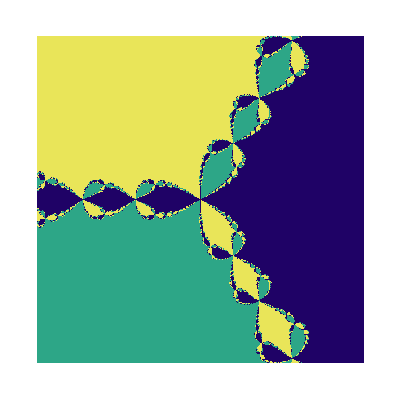

```mathematica
ArrayPlot[Transpose[resultado],ColorFunction->"BlueGreenYellow",FrameLabel->{"Im","Re"},BaseStyle->FontSize->14,FrameTicks->Automatic,DataRange->{{-2,2},{-2,2}}]
```

Ejercicio

El conjunto del Mandelbrot es una mapeo de números complejos cuya fórmula recursiva está dada por

z_(n+1) = z_n^2+c, donde c = z_0.

Se ha demostrado que si durante su órbita un punto cumple que |z_n| ≥ 2, entonces la condición inicial diverge. El conjunto de Mandelbrot en si es el conjunto de puntos que no divergen.

1) Graficar el conunto de Mandelbrot.
Hint:
Primero definir la matriz de condiciones iniciales c.
Luego iterarlos mediante la fórmula de Mandelbrot con 50 iteraciones.
Luego filtrarlos, para eso se puede hacer una función Piecewise que devuelva 0 cuando los puntos divergen y 1 cuando no divergen.
Por último se grafican con ArrayPlot.

```mathematica
δ = 0.01;
c = Table[x+ⅈ y,{x,-2,1,δ},{y,-1.5,1.5,δ }];
it = Nest[#^2+c &,c,50];
filter[z_]:= Piecewise[{{0,Abs[z]>2},{1,Abs[z]<2}}];

ArrayPlot[Transpose[Map[filter,it,{2}]]]
```

-Graphics-

2) Graficar el conjunto de Julia que es similar al conjunto de Mandelbrot pero se deja una c fija. En este caso se hará con c = -2.42	- i 0.59.